## E2 Number Visibility

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
series=(10#1+#2)&@@@Partition[RealDigits[E,10,2 10^6+1][[1,2;;]],2];
```

## SDL Complexity

```mathematica
<<sdl.mx
```

```mathematica
result=sdl[series]
```

{0.137858,0.964258}

## Visibility

```mathematica
<<visibility.mx
```

```mathematica
links=naturalVisibilityLinks[series];
```

```mathematica
natGraph=Graph[links, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[natGraph]//Mean//N]
```

```mathematica
count=VertexDegree[natGraph]//Counts
```

<|1→1,10→237,3→2093,7→488,6→672,8→394,12→154,24→10,2→2309,13→126,11→190,4→1436,5→1053,14→103,9→302,15→68,22→38,26→16,16→50,18→36,19→43,23→21,25→9,20→26,35→2,21→24,27→9,30→6,31→8,34→4,54→1,17→51,29→5,28→3,33→4,42→2,41→1,44→1,46→1,32→1,36→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

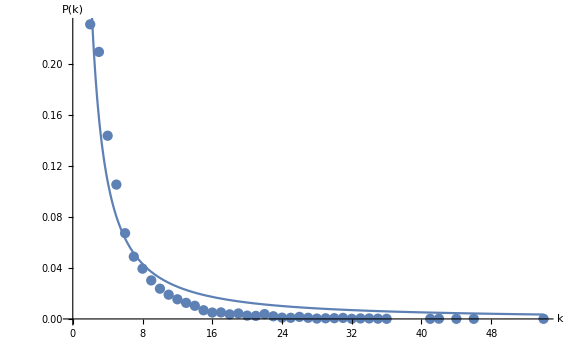
{{C→0.67297,γ→1.3212},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```

## Horizontal Visibility

```mathematica
horlinks=horizontalVisibilityLinks[series];
```

```mathematica
hg=Graph[horlinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
AppendTo[result,VertexDegree[hg]//Mean//N]
```

```mathematica
count=VertexDegree[hg]//Counts
```

<|1→1,5→936,3→2117,6→580,7→442,8→303,2→3641,9→210,11→90,4→1321,10→133,13→48,12→82,14→33,15→24,16→16,19→2,18→10,23→1,28→1,20→1,22→1,17→5,26→1|>

```mathematica
If[count[1]<3,count[1]=.];
```

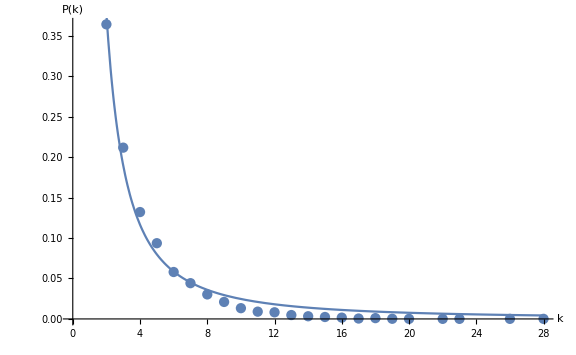
{{C→1.22107,γ→1.6951},-Graphics-}

```mathematica
m=plotModel[count,10000]
```

```mathematica
AppendTo[result,m[[1]]]
```